# Time Evolution

QuantumEvolvepaclet:Wolfram/QuantumFramework/ref/QuantumEvolveWolfram/QuantumFramework Package Symbol solves the equation of motion of a quantum system. Which equation that is depends on what you hand it: the Schrodinger equation for a closed system, the Lindblad master equation once jump operators are present, the Heisenberg equation when the thing being evolved is an operator, and the Kossakowski equation when the jump operators are correlated.

The call is the same shape in every case - a Hamiltonian, optionally some dissipation, an initial condition, and a time - and the result is always an object that depends on time. Supply a time to it and you get an ordinary state or operator back, which answers every property the framework knows about.

Two choices control everything else. A bare symbol for the time solves the equation exactly, through DSolvepaclet:ref/DSolve; a {t, t0, t1} interval solves it numerically, through NDSolvepaclet:ref/NDSolve. And an initial condition of Nonepaclet:ref/None evolves the propagator instead of any particular state, which can then be applied to whatever state you like.

```mathematica
<< Wolfram`QuantumFramework`
```

## A Driven Qubit

A PauliX Hamiltonian drives a qubit between 0 and 1. Evolving 0 over one full period:

```mathematica
psi = QuantumEvolve[QuantumOperator["PauliX"], QuantumState["0"], {t, 0, 2 Pi}]
```

QuantumState[…]

The result is a state as a function of time, and t is recorded on it as a parameter:

```mathematica
psi["Parameters"]
```

{t}

Supplying a time gives the state at that time - an ordinary QuantumStatepaclet:Wolfram/QuantumFramework/ref/QuantumStateWolfram/QuantumFramework Package Symbol with nothing left symbolic:

```mathematica
psi[1.]
```

QuantumState[…]

From there every state property is available as usual:

```mathematica
psi[1.]["ProbabilitiesList"]
```

{0.291927,0.708073}

Sampling the interval shows the population sloshing between the two levels and back:

```mathematica
Table[Round[psi[t]["ProbabilitiesList"], 0.0001], {t, 0, 3}]
```

{{1.,0.},{0.2919,0.7081},{0.1732,0.8268},{0.9801,0.0199}}

Plotting it gives the Rabi oscillation:

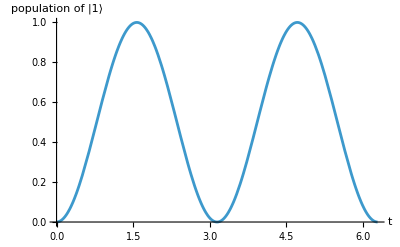

```mathematica
Plot[psi[t]["ProbabilitiesList"][[2]], {t, 0, 2 Pi},
    AxesLabel -> {"t", "population of |1⟩"}]
```

## What the Solution Actually Is

A numerically evolved state is not a table of samples and it is not a symbolic expression. Its amplitudes are the solver's own InterpolatingFunctionpaclet:ref/InterpolatingFunction, held as the state's array and applied to the time parameter:

```mathematica
psi["State"]
```

InterpolatingFunction[…][t]

That single object carries the whole two-component solution, so the state still knows its own shape without interpolating anything:

```mathematica
psi["Dimensions"]
```

{2}

Nothing is computed until a time is supplied; psi[1.] is what triggers an interpolation. This matters for large systems, where the alternative - one scalar interpolation per amplitude, each carrying its own copy of the solver's time grid - costs a copy of that grid per dimension. Asking for it explicitly with "Expand" -> True shows what is being avoided:

```mathematica
expanded = QuantumEvolve[QuantumOperator["PauliX"], QuantumState["0"], {t, 0, 2 Pi}, "Expand" -> True];
Normal[expanded["State"]]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

The two forms give the same numbers:

```mathematica
expanded[1.]["ProbabilitiesList"]
```

{0.291927,0.708073}

## Exact Solutions

Passing a bare symbol instead of an interval solves the equation symbolically rather than numerically:

```mathematica
exact = QuantumEvolve[QuantumOperator["PauliX"], QuantumState["0"], t];
Simplify[Normal[exact["StateVector"]]]
```

{Cos[t],-ⅈ Sin[t]}

That is the textbook solution, and its populations are what the plot above traced:

```mathematica
Simplify[exact["ProbabilitiesList"], Assumptions -> t ∈ Reals]
```

{Cos[t]^2,Sin[t]^2}

The initial state may be symbolic too, in which case so is the answer:

```mathematica
Simplify[Normal[QuantumEvolve[QuantumOperator["X"], QuantumState[{α, β}], t]["StateVector"]]]
```

{α Cos[t]-ⅈ β Sin[t],β Cos[t]-ⅈ α Sin[t]}

Omit the initial state and the time entirely and the register state 0 is used, with the formal symbol t as the time parameter. This is the shortest thing that says anything:

```mathematica
QuantumEvolve[QuantumOperator["X"]]
```

QuantumState[…]

The numerical solution agrees with the closed form to the solver's tolerance:

```mathematica
Max[Abs[psi[1.]["ProbabilitiesList"] - {Cos[1.] ^ 2, Sin[1.] ^ 2}]]
```

2.59879×10^-8

## Time-Dependent Hamiltonians

Nothing requires the Hamiltonian to be constant. A symbol in it that matches the evolution parameter simply makes the generator time dependent. This is a spin with splitting ω_0 driven transversally at the same frequency - a resonant drive:

```mathematica
ω0 = 2 Pi;
ωp = Pi/10;
tf = 2 Pi/ωp;
driven = ω0 QuantumOperator["JZ"] + 2 ωp Cos[ω0 t] QuantumOperator["JX"];
```

With no initial state given, the register state is used, so the Hamiltonian and the time interval are the whole call:

```mathematica
rabi = QuantumEvolve[driven, {t, 0, tf}]
```

QuantumState[…]

The Bloch vector traces the slow Rabi nutation underneath the fast Larmor precession. Over the interval 2π/ω_p it makes one full circuit from the north pole and back:

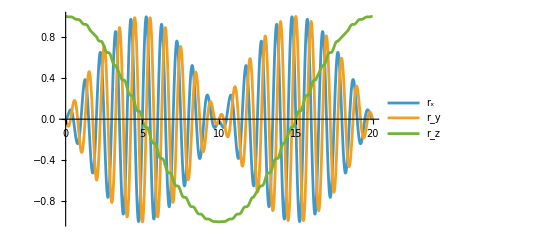

```mathematica
Plot[Evaluate[Re[rabi[t]["BlochVector"]]], {t, 0, tf}, PlotRange -> All,
    PlotLegends -> {Subscript[r, x], Subscript[r, y], Subscript[r, z]}]
```

Halfway through, the spin has been driven to the south pole - a π pulse:

```mathematica
Round[Chop[Re[rabi[tf/2]["BlochVector"]]], 0.0001]
```

{-0.025,-0.0002,-0.9997}

The evolution is unitary throughout, so the state stays pure and the Bloch vector stays on the sphere:

```mathematica
rabi[tf/2]["Purity"]
```

1

## Observables and Trajectories

An evolved state answers every ordinary state property once a time is given, so an observable is measured as it would be on any state:

```mathematica
QuantumMeasurement[QuantumMeasurementOperator[QuantumOperator["PauliZ"]] @ psi[1.]]["Mean"]
```

-0.416147

For a qubit the Bloch vector gives the motion directly. Under PauliX the state precesses about the x axis, so the x component stays zero:

```mathematica
Chop[psi[1.]["BlochCartesianCoordinates"]]
```

{0,-0.909297,-0.416147}

Drawing that as a curve on the Bloch sphere shows the precession as the great circle it is:

```mathematica
Show[QuantumState["UniformMixture"]["BlochPlot"],
    ParametricPlot3D[Evaluate[Re[psi[t]["BlochVector"]]], {t, 0, 2 Pi}]]
```

-Graphics3D-

## Open Systems: the Lindblad Equation

Jump operators turn the Schrodinger equation into the Lindblad master equation,

∂_t ρ=-i[H,ρ]+∑_i γ_i(L_i ρ L_i^†-1/2{L_i^†L_i,ρ}),

with ρ the density matrix, L_i the jump operators and γ_i their rates. Passing them as Ls -> rates is enough to switch equations. Here a PauliZ Hamiltonian with PauliX dephasing at rate 0.6:

```mathematica
noisy = QuantumEvolve[QuantumOperator["PauliZ"], {QuantumOperator["PauliX"]} -> {0.6},
    QuantumState["0"], {t, 0, 3}]
```

QuantumState[…]

The state is a density matrix now rather than a vector, because dissipation does not preserve purity. Purity falls from 1 toward the maximally mixed value of 1/2:

```mathematica
Table[noisy[t]["Purity"], {t, 0, 3}]
```

{1.,0.545359,0.504115,0.500373}

The populations equalize as it goes:

```mathematica
noisy[3.]["ProbabilitiesList"]
```

{0.513662,0.486338}

## Relaxing to a Thermal State

Dephasing drives a qubit to the maximally mixed state because it has no preferred direction. Amplitude damping does have one, and at finite temperature the two directions compete. With a mean occupation n of the bath, decay happens at rate γ(n+1) and absorption at rate γn:

```mathematica
Ω = 50; γ = 1; n = 3;
H = Ω/2 QuantumOperator["Z"];
σm = QuantumOperator[{{0, 1}, {0, 0}}];
Ls = {σm, σm["Dagger"]};
γs = γ {n + 1, n};
```

Starting from a pure state tilted off the axis:

```mathematica
ρ0 = QuantumState[{Cos[Pi/8], Exp[I Pi/4] Sin[Pi/8]}]
```

QuantumState[…]

```mathematica
ρt = QuantumEvolve[H, Ls -> γs, ρ0, {t, 0, 1}]
```

QuantumState[…]

By t=1 the populations have all but reached the thermal ratio {(n+1)/(2n+1), n/(2n+1)}, which for n=3 is {4/7,3/7}:

```mathematica
ρt[1.]["ProbabilitiesList"]
```

{0.571686,0.428314}

```mathematica
N[{n + 1, n}/(2 n + 1)]
```

{0.571429,0.428571}

The trajectory spirals in from the surface of the Bloch sphere toward that point, the fast PauliZ precession winding around the slow decay:

```mathematica
Show[QuantumState["UniformMixture"]["BlochPlot"],
    ParametricPlot3D[Evaluate[Re[ρt[t]["BlochVector"]]], {t, 0, 1}]]
```

-Graphics3D-

The rates can equally be folded into the operators as √γ_i L_i, in which case the jump operators are given as a plain list and the result is identical:

```mathematica
ρt2 = QuantumEvolve[H, Sqrt[γs] Ls, ρ0, {t, 0, 1}];
Max[Abs[Normal[ρt2[1.]["DensityMatrix"]] - Normal[ρt[1.]["DensityMatrix"]]]]
```

0.

## The Liouvillian and the Propagator

An open-system generator can be assembled on its own as a Liouvillian superoperator ℒ, the object with dρ/dt=ℒρ:

```mathematica
ℒ = QuantumOperator["Liouvillian"[QuantumOperator["Z"], {σm}, {0.3}]]
```

QuantumOperator[…]

It acts on a density matrix flattened into a vector, so for a qubit its matrix is 4x4 rather than 2x2:

```mathematica
Dimensions[ℒ["Matrix"]]
```

{4,4}

Passing Nonepaclet:ref/None in place of an initial state evolves the propagator rather than any particular state. Given a Liouvillian this produces e^ℒt, the map that takes any initial density matrix to its state at time t:

```mathematica
U = QuantumEvolve[I ℒ, None, {t, 0, 5}]
```

QuantumOperator[…]

Because it is the map and not a trajectory, it can be applied to any state without solving again:

```mathematica
ρstart = QuantumState[{Cos[Pi/8], Sin[Pi/8]}];
U[2.][ρstart]["ProbabilitiesList"]
```

{0.919628,0.0803716}

Solving the same problem directly as a Lindblad equation gives the same answer, to the solver's tolerance:

```mathematica
QuantumEvolve[QuantumOperator["Z"], {σm} -> {0.3}, ρstart, {t, 0, 5}][2.]["ProbabilitiesList"]
```

{0.919628,0.0803716}

The propagator also exists for closed systems, where it is the familiar unitary. Solved exactly it is a closed form:

```mathematica
Simplify[Normal[QuantumEvolve[QuantumOperator["PauliX"], None, t]["Matrix"]]]
```

{{Cos[t],-ⅈ Sin[t]},{-ⅈ Sin[t],Cos[t]}}

## The Heisenberg Picture

The same superoperator run backwards evolves observables instead of states. Taking its adjoint and applying it to an operator - passed through QuantumStatepaclet:Wolfram/QuantumFramework/ref/QuantumStateWolfram/QuantumFramework Package Symbol as a matrix state, then read back as an operator - gives A(t):

```mathematica
A0 = QuantumOperator["Z"];
At = U["Dagger"][A0["MatrixQuantumState"]]["Operator"];
```

The two pictures are two ways of writing the same number, Tr[A_0 ρ(t)]=Tr[A(t)ρ_0]. In the Schrodinger picture the state moves:

```mathematica
Re[Tr[Normal[A0["Matrix"]] . Normal[U[2.][ρstart]["DensityMatrix"]]]]
```

0.839257

In the Heisenberg picture the observable moves and the state does not:

```mathematica
Re[Tr[Normal[At[2.]["Matrix"]] . Normal[ρstart["DensityMatrix"]]]]
```

0.839257

They agree to machine precision across the interval, since both read the same solved propagator:

```mathematica
Max[Table[Abs[Tr[Normal[A0["Matrix"]] . Normal[U[t][ρstart]["DensityMatrix"]]] -
    Tr[Normal[At[t]["Matrix"]] . Normal[ρstart["DensityMatrix"]]]], {t, 0, 5, 0.5}]]
```

1.11022×10^-16

## The Kossakowski Equation

The Lindblad equation assumes the jump operators are uncorrelated. Dropping that assumption gives the Kossakowski equation,

∂_t ρ=-i[H,ρ]+∑_ij β_ij(L_i ρ L_j^†-1/2{L_j^†L_i,ρ}),

where the rates become a positive-semidefinite matrix β_ij whose off-diagonal entries encode correlations between channels. A diagonal β recovers the Lindblad equation. Building the Liouvillian with a matrix in place of a list of rates is all it takes.

Two atoms decaying into a shared field is the standard example. The Hamiltonian is just their bare energies:

```mathematica
ω1 = 0.9; ω2 = 0.7;
Hk = QuantumOperator[ω1/2 "ZI" + ω2/2 "IZ"];
```

Each atom decays through its own lowering operator:

```mathematica
jumpOps = QuantumTensorProduct[QuantumOperator[#], QuantumOperator[#2]] & @@@ {{"-", "I"}, {"I", "-"}}
```

{QuantumOperator[…],QuantumOperator[…]}

The correlation between the two channels is the off-diagonal γ_12; the matrix is positive semidefinite as long as γ≥γ_12:

```mathematica
γd = 0.5; γ12 = 0.45;
β = {{γd, γ12}, {γ12, γd}};
ℒk = QuantumOperator["Liouvillian"[Hk, jumpOps, β]];
Dimensions[ℒk["Matrix"]]
```

{16,16}

Evolve three initial states with one excitation between them - a product state, the singlet, and the triplet. When the Hamiltonian is already a superoperator, the initial state comes directly after it:

```mathematica
states = QuantumState /@ {"01", "PsiMinus", "PsiPlus"};
evolved = QuantumEvolve[I ℒk, #, {t, 0, 5}] & /@ states;
```

Count the excitations left at each time with the total-number operator:

```mathematica
totalExcitation = Total @ With[{mat = {{1, 0}, {0, 0}}}, Array[QuantumOperator[mat, {#}] &, 2]];
excitations = Table[Re[Tr[Normal[#[t]["DensityMatrix"]] . Normal[totalExcitation["Matrix"]]]],
    {t, 0, 5, 0.05}] & /@ evolved;
```

All three start with one excitation and all three decay, but at three different rates. The correlation splits the symmetric and antisymmetric combinations apart: the singlet is subradiant, decaying at γ-γ_12, and the triplet is superradiant, decaying at γ+γ_12 - here a factor of nineteen between them:

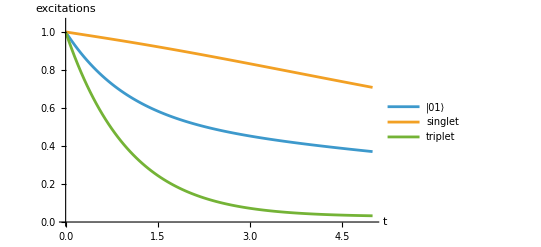

```mathematica
ListLinePlot[excitations, DataRange -> {0, 5}, PlotRange -> {0, 1.05},
    PlotLegends -> {"|01⟩", "singlet", "triplet"},
    AxesLabel -> {"t", "excitations"}]
```

At the end of the interval they are far apart:

```mathematica
Round[excitations[[All, -1]], 0.0001]
```

{0.3705,0.7082,0.0327}

## Watching for Events

"AdditionalEquations" injects extra equations or specifications into the solve, which is how hybrid and piecewise systems are expressed - and how events are detected. Here a strong pulsed drive with a constant detuning:

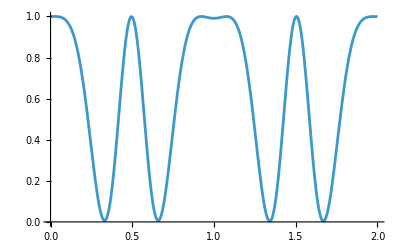

```mathematica
rabiDrive = 10. Sin[Pi t] QuantumOperator["X"] - QuantumState["1"]["Operator"];
pulsed = QuantumEvolve[rabiDrive, {t, 0, 2}];
Plot[pulsed[t]["Probability"][[1]], {t, 0, 2}, PlotRange -> {0, 1}]
```

To find the times at which the population crosses one half, solve again with a WhenEventpaclet:ref/WhenEvent. The dependent variable of the internal differential equation is the formal symbol s, so the condition is written on Indexed[s[t], 1], and Sowpaclet:ref/Sow/Reappaclet:ref/Reap collect the crossings:

```mathematica
{sol, points} = Reap @ QuantumEvolve[rabiDrive, {t, 0, 5},
    "AdditionalEquations" -> WhenEvent[Abs[Indexed[s[t], 1]] ^ 2 == 0.5, Sow[t]]];
Length[First[points]]
```

20

```mathematica
Round[Take[First[points], 4], 0.0001]
```

{0.2287,0.4156,0.5747,0.7573}

The crossings really are crossings - evaluating the returned solution at them gives one half back:

```mathematica
Max[Abs[(sol[#]["Probability"][[1]] & /@ First[points]) - 0.5]]
```

1.78399×10^-6

Shading the plot between them marks out the intervals where the qubit is mostly excited:

Mesh::ilevels: 0.22871 is not a valid mesh specification.

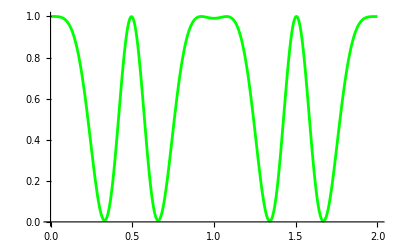

```mathematica
Plot[sol[t]["Probability"][[1]], {t, 0, 2}, Mesh -> First[points],
    MeshShading -> {Green, Orange}, PlotRange -> {0, 1}]
```

## The Equations Themselves

"ReturnEquations" -> True stops short of solving and hands back the system instead, in exactly the form the solver would have been called with - equations, dependent variable, and time specification:

```mathematica
QuantumEvolve[QuantumOperator["XX"], {t, 0, 1}, "ReturnEquations" -> True]
```

{{s'[t]==SparseArray[…].s[t],s[0]==SparseArray[…]},s,{t,0,1}}

The generator is right there in the equation, and it is exactly -iH for the Hamiltonian that went in - here -i X⊗X:

```mathematica
eqs = QuantumEvolve[QuantumOperator["XX"], {t, 0, 1}, "ReturnEquations" -> True];
MatrixForm[Normal[eqs[[1, 1, 2, 1]]]]
```

(0 | 0 | 0 | -ⅈ
0 | 0 | -ⅈ | 0
0 | -ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0)

Reaching for this is worthwhile when the system needs to be handed to a solver directly - to couple it to equations of a different kind, to pick a Methodpaclet:ref/Method by hand, or simply to see what is being integrated.

The triple is in NDSolveValuepaclet:ref/NDSolveValue's argument order, but two things in it are for the framework's benefit rather than the solver's: the matrices are sparse, which NDSolveValuepaclet:ref/NDSolveValue will not accept as an initial condition, and the dependent variable is a formal symbol. Make both ordinary and it runs:

```mathematica
solved = NDSolveValue @@ (eqs /. {sa_SparseArray :> Normal[sa], s -> s})
```

InterpolatingFunction[…]

What comes back is the same solution QuantumEvolvepaclet:Wolfram/QuantumFramework/ref/QuantumEvolveWolfram/QuantumFramework Package Symbol would have handed over wrapped in a state - 00 rotating into 11 as cos t and -isin t:

```mathematica
Chop[solved[1.]]
```

{0.540302,0,0,0.-0.841471 ⅈ}

## Details

The time argument is either a symbol, which solves the equation exactly with DSolvepaclet:ref/DSolve, or {t, t0, t1}, which solves it numerically with NDSolvepaclet:ref/NDSolve. Options not recognized by QuantumEvolvepaclet:Wolfram/QuantumFramework/ref/QuantumEvolveWolfram/QuantumFramework Package Symbol are passed through to whichever solver runs, so AccuracyGoal, Method, MaxSteps and the rest all work.

The initial condition selects the equation. A state gives the Schrodinger or Lindblad equation; an operator gives the Heisenberg equation; Nonepaclet:ref/None gives the propagator. Omitting it uses the register state 0…0, and omitting the time along with it uses the formal symbol t.

Jump operators are given either as {L1, L2, ...} -> {γ1, γ2, ...} or as a plain list with the rates folded in as √γ_i L_i. Correlated channels need the Kossakowski form, which is reached by building QuantumOperator["Liouvillian"[H, Ls, β]] with a rate matrix and evolving I ℒ.

With a Hamiltonian that is already a superoperator, the state argument comes directly after it: QuantumEvolve[ℒ, state, {t, 0, 2}].

The evolution parameter is recorded on the returned object, so state["Parameters"] names it and state[t] supplies it.

A numerically evolved state holds the solver's InterpolatingFunctionpaclet:ref/InterpolatingFunction as its amplitudes, so it answers questions about its shape without evaluating anything, and interpolation happens once a time is supplied. "Expand" -> True instead stores one scalar interpolation per amplitude, each carrying its own copy of the solver's time grid.

"MergeInterpolatingFunctions" controls what happens when the Hamiltonian itself contains interpolating functions of time. The default merges them into a single sparse interpolation, which is substantially faster than letting each enter the dynamical equation separately.

## Possible Issues

Ask for amplitudes before supplying a time and the answer is a function of the parameter rather than numbers, which is rarely what is wanted from a numerical solve. Supply the time first:

```mathematica
psi[0.5]["ProbabilitiesList"]
```

{0.770151,0.229849}

The numerical and exact routes agree to the solver's tolerance, not to machine precision, and the difference above is around the eighth decimal. Tighten it with the usual NDSolvepaclet:ref/NDSolve options.

Defining a time-dependent Hamiltonian as a function of its time argument does not work the way it looks like it should. The operator's matrix is a SparseArraypaclet:ref/SparseArray, and a pattern variable is not substituted into it, so the symbol in the stored expression is never replaced:

```mathematica
badH[x_] = Sin[x] QuantumOperator["X"];
Normal[badH[0.3]["Matrix"]]
```

{{0,Sin[x]},{Sin[x],0}}

Write the Hamiltonian as a plain expression in the evolution parameter instead, and let QuantumEvolvepaclet:Wolfram/QuantumFramework/ref/QuantumEvolveWolfram/QuantumFramework Package Symbol handle the substitution:

```mathematica
Normal[(Sin[t] QuantumOperator["X"])["Matrix"]]
```

{{0,Sin[t]},{Sin[t],0}}

If the exact solver cannot find a closed form, the output is the unevaluated solver call it gave up on, along with a message. Here a Rabi problem with a general detuning, which has no elementary solution:

```mathematica
QuantumEvolve[1/2 Subscript[ω, 0] QuantumOperator["Z"] +
    γr Cos[Subscript[ω, p] t] QuantumOperator["X"], t]
```

QuantumEvolve::error: Differential Solver failed to find a solution

DSolveValue[{s'[t]=={{-(ⅈ ω_0)/2,-1/2 ⅈ ⅇ^(-ⅈ t ω_p) γr-1/2 ⅈ ⅇ^(ⅈ t ω_p) γr},{-1/2 ⅈ ⅇ^(-ⅈ t ω_p) γr-1/2 ⅈ ⅇ^(ⅈ t ω_p) γr,(ⅈ ω_0)/2}}.s[t],s[0]=={1,0}},s[t]∈Vectors[2,ℂ],t,{}]

Numbers in the Hamiltonian make the same problem solvable numerically, so the fallback when a closed form does not exist is to give the parameters values and pass an interval instead.

Related Guides

WolframQuantumComputationFrameworkpaclet:Wolfram/QuantumFramework/guide/WolframQuantumComputationFramework

Related Tech Notes

GettingStartedpaclet:Wolfram/QuantumFramework/tutorial/GettingStarted ▪ QuantumMachineLearningpaclet:Wolfram/QuantumFramework/tutorial/QuantumMachineLearning

## Metadata

### Categorization

Tutorial

Wolfram/QuantumFramework

Wolfram`QuantumFramework`

Wolfram/QuantumFramework/tutorial/TimeEvolution

### Keywords

QuantumEvolve

Schrodinger equation

Lindblad

Liouvillian

Kossakowski

open system

propagator

Rabi oscillation

decoherence

Bloch vector

Heisenberg picture

superradiance